```mathematica
Clear[Lx, Ly, A, l, mL,
 SX2DSingDis,SY2DSingDis,
 CX2DSingDis,CY2DSingDis,
 Cons]
```

```mathematica
Lx = 20;
Ly = 20;
l = 10;
mL = 10;
A = Lx*Ly + Ly-l
NOrbitals = 2*A;
```

410

```mathematica
(**------------------------------------**)
```

```mathematica
SX2DSingDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{SX2DSingDis[[a + b Lx, a + 1 + b Lx]]=I/2, SX2DSingDis[[a + 1 + b Lx, a + b Lx]] = -I/2},{a,1, Lx -1}],{b,0, l-1}]
Do[Do[{SX2DSingDis[[a+b (Lx+1)+l *Lx,a+1+b (Lx+1)+l *Lx]]=I/2, SX2DSingDis[[a+b (Lx+1)+l *Lx+1,a+b (Lx+1)+l *Lx]]=-I/2},{a,1,Lx}],{b,0,Ly-1-l}]
```

```mathematica
(**------------------------------------**)
```

```mathematica
CX2DSingDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{CX2DSingDis[[a + b Lx, a + 1 + b Lx]]=1/2, CX2DSingDis[[a + 1 + b Lx, a + b Lx]] = 1/2},{a,1, Lx -1}],{b,0, l-1}]
Do[Do[{CX2DSingDis[[a+b (Lx+1)+l *Lx,a+1+b (Lx+1)+l *Lx]]=1/2, CX2DSingDis[[a+b (Lx+1)+l *Lx+1,a+b (Lx+1)+l *Lx]]=1/2},{a,1,Lx}],{b,0,Ly-1-l}]
```

```mathematica
(**------------------------------------**)
```

```mathematica
SY2DSingDis=Table[0,{a,1,A},{b,1,A}];
(**lower block**)
Do[Do[{SY2DSingDis[[a + b Lx, a + (1+ b) Lx]]=I/2, SY2DSingDis[[a +(1 + b) Lx, a + b Lx]] = -I/2},{a,1, Lx }],{b,0, l-2}]
(**upper block**)
Do[Do[{SY2DSingDis[[a + b (Lx+1)+l*Lx, a + (b+1) (Lx+1)+l*Lx]]=I/2, SY2DSingDis[[a + (b+1) (Lx+1)+l*Lx, a + b (Lx+1)+l*Lx]] = -I/2},{a,1, Lx+1 }],{b,0, Ly-l-2}]
(**connectors**)
Do[{SY2DSingDis[[a + (l-1)*Lx, a +l*Lx]]=I/2, SY2DSingDis[[a +l*Lx, a +(l-1)*Lx]] = -I/2},{a,1,mL }]
Do[{SY2DSingDis[[a + mL+(l-1)*Lx, a +mL+1+l*Lx]]=I/2, SY2DSingDis[[a +mL+1+l*Lx, a + mL+(l-1)*Lx]] = -I/2},{a,1,Lx-mL }]
```

```mathematica
(**------------------------------------**)
```

```mathematica
CY2DSingDis=Table[0,{a,1,A},{b,1,A}];
(**lower block**)
Do[Do[{CY2DSingDis[[a + b Lx, a + (1+ b) Lx]]=1/2, CY2DSingDis[[a +(1 + b) Lx, a + b Lx]] = 1/2},{a,1, Lx }],{b,0, l-2}]
(**upper block**)
Do[Do[{CY2DSingDis[[a + b (Lx+1)+l*Lx, a + (b+1) (Lx+1)+l*Lx]]=1/2, CY2DSingDis[[a + (b+1) (Lx+1)+l*Lx, a + b (Lx+1)+l*Lx]] = 1/2},{a,1, Lx+1 }],{b,0, Ly-l-2}]
(**connectors**)
Do[{CY2DSingDis[[a + (l-1)*Lx, a +l*Lx]]=1/2, CY2DSingDis[[a +l*Lx, a +(l-1)*Lx]] = 1/2},{a,1,mL }]
Do[{CY2DSingDis[[a + mL+(l-1)*Lx, a +mL+1+l*Lx]]=1/2, CY2DSingDis[[a +mL+1+l*Lx, a + mL+(l-1)*Lx]] = 1/2},{a,1,Lx-mL }]
```

```mathematica
(**------------------------------------**)
```

```mathematica
Cons=Table[0,{a,1,A},{b,1,A}];
Do[Cons[[a,a]]=1,{a,1,A}]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHIDisloc]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHIDisloc[t_,t0_,m_]:=t*(KroneckerProduct[SX2DSingDis,σ1]+KroneckerProduct[SY2DSingDis, σ2])+KroneckerProduct[-m*Cons+t0*(CX2DSingDis+CY2DSingDis),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHIDisloc[1.0,1.0,1.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

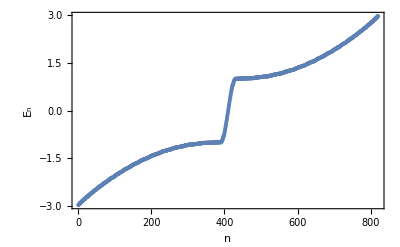

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],(*Plot[0,{x,0,2A},PlotStyle-> Red],*)BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
(**---------------------------------------------------------**)
```

```mathematica
Clear[Xaxis, Yaxis1, Yaxis2, Yaxis3, P3, P4, P2B]
```

```mathematica
Xaxis=Table[{{1,j},{Lx+1,j}},{j,1,Ly,1}];
```

```mathematica
Dimensions[Xaxis]
```

{20,2,2}

```mathematica
P3=Graphics[ListPlot[Table[Xaxis[[j]],{j,1,Ly}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,28/2,29},None}},BaseStyle-> 18];
```

```mathematica
Yaxis1=Table[{{j,1},{j,Ly}},{j,1,mL,1}];
```

```mathematica
Yaxis2={{mL+1,l+1},{mL+1,Ly}};
```

```mathematica
Yaxis3=Table[{{j,1},{j,Ly}},{j,mL+2,Lx+1,1}];
```

```mathematica
Dimensions[Yaxis3]
```

{10,2,2}

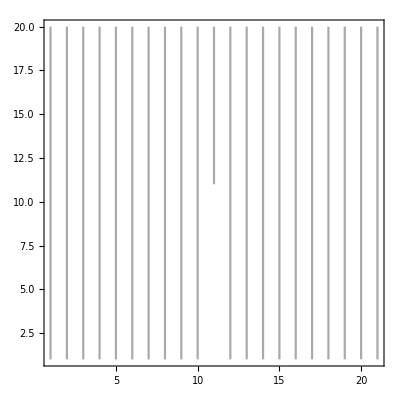

```mathematica
P4=Show[ListPlot[Table[Yaxis1[[j]],{j,1,mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
ListPlot[Yaxis2,Joined-> True,PlotStyle-> Lighter[Gray]],
ListPlot[Table[Yaxis3[[j]],{j,1,Lx-mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}}]
]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P2B=Show[Graphics[{},

Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,Round[Ly/4]+1,Round[3 Ly/4],Ly},None},{{1,Round[Lx/2]+1,Lx+1},None}},BaseStyle-> 18,
PlotRange-> {{1,Lx+1},{1,Ly}}
]]
```

-Graphics-

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

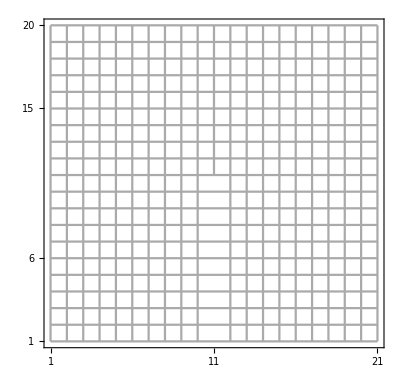

```mathematica
P5=Show[P2B,P3,P4]
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+0
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-1
```

```mathematica
N[LineUp[6]]
```

3.09017

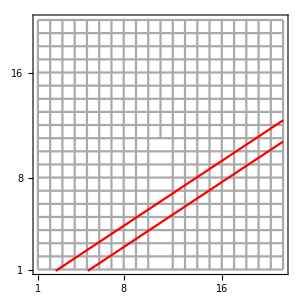

```mathematica
Show[P5,
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+1+0.1}}],
Plot[LineDn[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+1+0.1}}],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"}},None}},
ImageSize-> 300,AspectRatio-> 1
]
```

```mathematica
(**---This function generates site number for a given coordinates and set of parameter---**)
```

```mathematica
(**---Generates 0 for non existing points, e.g. the two lines below and above dislocation centers---**)
```

```mathematica
GenerateSiteNumber[x_,y_,Lx_,Ly_,l_,mL_]:=Piecewise[{{x+(y-1)Lx, 1≤ x ≤ mL &&1≤ y≤ l },{x+(y-1)Lx-1, Lx+1≥ x > mL+1 &&1≤ y≤ l},{x+(y-1)(Lx+1)-l,l<y≤Ly&&Lx+1≥ x ≥ 1 }},0]
```

```mathematica
GenerateSiteNumber[11,9,Lx,Ly,l,mL]
```

0

```mathematica
Clear[FibonListNew]
FibonListNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
(**--x runs from 1 to Lx + 1--**)
```

```mathematica
Do[Do[FibonListNew=Append[FibonListNew,GenerateSiteNumber[x,y,Lx,Ly,l,mL]],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx+1}]
```

```mathematica
FibonList=Sort[FibonListNew]
```

{0,0,3,4,5,25,26,46,47,48,68,69,70,90,111,112,132,133,153,154,155,175,176,177,197,198,219,220,221,242}

```mathematica
(**--Delete the zeros, which are generated for the non-existing lines of atoms--**)
```

```mathematica
FibonList=DeleteCases[FibonList,0]
```

{3,4,5,25,26,46,47,48,68,69,70,90,111,112,132,133,153,154,155,175,176,177,197,198,219,220,221,242}

```mathematica
Dimensions[FibonList]
```

{28}

```mathematica
Clear[Fibonup, Fibondown, TotalFibon]
```

```mathematica
Fibonup = 2 * FibonList -1;
```

```mathematica
Fibondown = 2* FibonList;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon=Sort[TotalFibon];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

56

```mathematica
NOrbitalsQuasi/2
```

43

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

764

```mathematica
(*-----------------------------------------------------------------------------*)
```